## MATH-459

## Presentation #2

# Problems 71 and 72

Goal: To generate the boundary points for  a matrix A, and use these to sketch the numerical range. 
By problem 69, we know these boundary points are of the form  ⟨Av(t), v(t)⟩,  where t∈[0, 2π), and v(t) is the unit eigenvector corresponding to the maximum eigenvalue p(t) of the matrix Re(e^-itA). 
Step 1: Generate a table of angles t from 0 to 2π, in increments of 100. 
Step 2: For a given matrix A and a given value of t, compute the maximum eigenvalue p(t) of Re(e^-itA).
Step 3: Compute the corresponding eigenvector.
Step 4: Compute the associated boundary point,  ⟨Av(t), v(t)⟩.
Step 5: Do this for each each t between 0 and 2π.

```mathematica
ts=Table[t, {t, 0, 2π, 1/100}]
```

{0,1/100,1/50,3/100,1/25,1/20,3/50,7/100,2/25,9/100,1/10,11/100,3/25,13/100,7/50,3/20,4/25,17/100,9/50,19/100,1/5,21/100,11/50,23/100,6/25,1/4,13/50,27/100,7/25,29/100,3/10,31/100,8/25,33/100,17/50,7/20,9/25,37/100,19/50,39/100,2/5,41/100,21/50,43/100,11/25,9/20,23/50,47/100,12/25,49/100,1/2,51/100,13/25,53/100,27/50,11/20,14/25,57/100,29/50,59/100,3/5,61/100,31/50,63/100,16/25,13/20,33/50,67/100,17/25,69/100,7/10,71/100,18/25,73/100,37/50,3/4,19/25,77/100,39/50,79/100,4/5,81/100,41/50,83/100,21/25,17/20,43/50,87/100,22/25,89/100,9/10,91/100,23/25,93/100,47/50,19/20,24/25,97/100,49/50,99/100,1,101/100,51/50,103/100,26/25,21/20,53/50,107/100,27/25,109/100,11/10,111/100,28/25,113/100,57/50,23/20,29/25,117/100,59/50,119/100,6/5,121/100,61/50,123/100,31/25,5/4,63/50,127/100,32/25,129/100,13/10,131/100,33/25,133/100,67/50,27/20,34/25,137/100,69/50,139/100,7/5,141/100,71/50,143/100,36/25,29/20,73/50,147/100,37/25,149/100,3/2,151/100,38/25,153/100,77/50,31/20,39/25,157/100,79/50,159/100,8/5,161/100,81/50,163/100,41/25,33/20,83/50,167/100,42/25,169/100,17/10,171/100,43/25,173/100,87/50,7/4,44/25,177/100,89/50,179/100,9/5,181/100,91/50,183/100,46/25,37/20,93/50,187/100,47/25,189/100,19/10,191/100,48/25,193/100,97/50,39/20,49/25,197/100,99/50,199/100,2,201/100,101/50,203/100,51/25,41/20,103/50,207/100,52/25,209/100,21/10,211/100,53/25,213/100,107/50,43/20,54/25,217/100,109/50,219/100,11/5,221/100,111/50,223/100,56/25,9/4,113/50,227/100,57/25,229/100,23/10,231/100,58/25,233/100,117/50,47/20,59/25,237/100,119/50,239/100,12/5,241/100,121/50,243/100,61/25,49/20,123/50,247/100,62/25,249/100,5/2,251/100,63/25,253/100,127/50,51/20,64/25,257/100,129/50,259/100,13/5,261/100,131/50,263/100,66/25,53/20,133/50,267/100,67/25,269/100,27/10,271/100,68/25,273/100,137/50,11/4,69/25,277/100,139/50,279/100,14/5,281/100,141/50,283/100,71/25,57/20,143/50,287/100,72/25,289/100,29/10,291/100,73/25,293/100,147/50,59/20,74/25,297/100,149/50,299/100,3,301/100,151/50,303/100,76/25,61/20,153/50,307/100,77/25,309/100,31/10,311/100,78/25,313/100,157/50,63/20,79/25,317/100,159/50,319/100,16/5,321/100,161/50,323/100,81/25,13/4,163/50,327/100,82/25,329/100,33/10,331/100,83/25,333/100,167/50,67/20,84/25,337/100,169/50,339/100,17/5,341/100,171/50,343/100,86/25,69/20,173/50,347/100,87/25,349/100,7/2,351/100,88/25,353/100,177/50,71/20,89/25,357/100,179/50,359/100,18/5,361/100,181/50,363/100,91/25,73/20,183/50,367/100,92/25,369/100,37/10,371/100,93/25,373/100,187/50,15/4,94/25,377/100,189/50,379/100,19/5,381/100,191/50,383/100,96/25,77/20,193/50,387/100,97/25,389/100,39/10,391/100,98/25,393/100,197/50,79/20,99/25,397/100,199/50,399/100,4,401/100,201/50,403/100,101/25,81/20,203/50,407/100,102/25,409/100,41/10,411/100,103/25,413/100,207/50,83/20,104/25,417/100,209/50,419/100,21/5,421/100,211/50,423/100,106/25,17/4,213/50,427/100,107/25,429/100,43/10,431/100,108/25,433/100,217/50,87/20,109/25,437/100,219/50,439/100,22/5,441/100,221/50,443/100,111/25,89/20,223/50,447/100,112/25,449/100,9/2,451/100,113/25,453/100,227/50,91/20,114/25,457/100,229/50,459/100,23/5,461/100,231/50,463/100,116/25,93/20,233/50,467/100,117/25,469/100,47/10,471/100,118/25,473/100,237/50,19/4,119/25,477/100,239/50,479/100,24/5,481/100,241/50,483/100,121/25,97/20,243/50,487/100,122/25,489/100,49/10,491/100,123/25,493/100,247/50,99/20,124/25,497/100,249/50,499/100,5,501/100,251/50,503/100,126/25,101/20,253/50,507/100,127/25,509/100,51/10,511/100,128/25,513/100,257/50,103/20,129/25,517/100,259/50,519/100,26/5,521/100,261/50,523/100,131/25,21/4,263/50,527/100,132/25,529/100,53/10,531/100,133/25,533/100,267/50,107/20,134/25,537/100,269/50,539/100,27/5,541/100,271/50,543/100,136/25,109/20,273/50,547/100,137/25,549/100,11/2,551/100,138/25,553/100,277/50,111/20,139/25,557/100,279/50,559/100,28/5,561/100,281/50,563/100,141/25,113/20,283/50,567/100,142/25,569/100,57/10,571/100,143/25,573/100,287/50,23/4,144/25,577/100,289/50,579/100,29/5,581/100,291/50,583/100,146/25,117/20,293/50,587/100,147/25,589/100,59/10,591/100,148/25,593/100,297/50,119/20,149/25,597/100,299/50,599/100,6,601/100,301/50,603/100,151/25,121/20,303/50,607/100,152/25,609/100,61/10,611/100,153/25,613/100,307/50,123/20,154/25,617/100,309/50,619/100,31/5,621/100,311/50,623/100,156/25,25/4,313/50,627/100,157/25}

```mathematica
GetEval[A_, t_]:=Max[Re[Eigenvalues[(Exp[-I t ]* A+ConjugateTranspose[Exp[-I t ]*A])/2]]]//N
```

```mathematica
(* Note:ReA=(A+A^*)/2, so Re(e^-it A)= (e^-it A + e^-it A^*)/2. So this function finds our maximum eigenvalue p(t) for a given value of t. *)
```

```mathematica
GetEvect[A_, t_]:= N[(NullSpace[((Exp[-I t]A+ConjugateTranspose[Exp[-I t ]A])/2)-(GetEval[A, t]IdentityMatrix[Length[A]])][[1]])/Norm[NullSpace[((Exp[-I t]A+ConjugateTranspose[Exp[-I t ]A])/2)-(GetEval[A, t]IdentityMatrix[Length[A]])][[1]]]]
```

```mathematica
(* This function finds a vector V in the Nullspace of Re(e^-it A)-p(t)I, which is our corresponding eigenvector to p(t), and then divides it by the Norm of V to make it our unit eigenvector v(t) *)
```

```mathematica
GetBoundary[A_, t_]:= N[{Re[Dot[A.GetEvect[A, t], Conjugate[GetEvect[A, t]]]],Im[Dot[A.GetEvect[A, t], Conjugate[GetEvect[A, t]]]]} ]
```

```mathematica
(* This function computes ⟨Av(t),v(t)⟩. Note that ⟨Av(t),v(t)⟩=Av(t).OverBar[v(t)] *)
```

```mathematica
GetNumRange[A_]:= (pts={};For[i=1, i<=Length[ts], i++, AppendTo[pts,GetBoundary[N[A], ts[[i]]]]];pts)
```

```mathematica
(* This function iterates over all our t values and generates of list of all of our boundary points ⟨Av(t),v(t)⟩ *)
```

```mathematica
ListLinePlot[GetNumRange[{{I, 0}, {2, 3-5 I}}]]
```

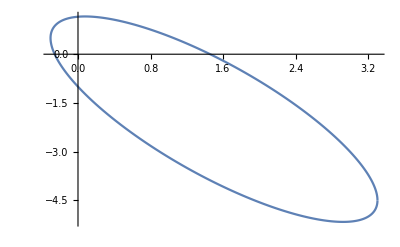

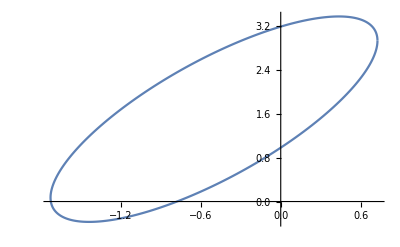

```mathematica
ListLinePlot[GetNumRange[{{-1, 2}, {I, 3I}}]]
```

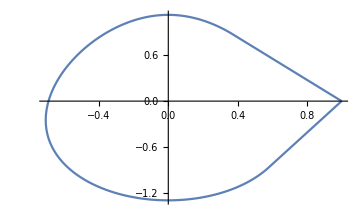

```mathematica
ListLinePlot[GetNumRange[{{1, 0, 0, 0}, {0, I, 0, 0}, {0, 0, 0, -1}, {0, 1, 0, -I}}]]
```

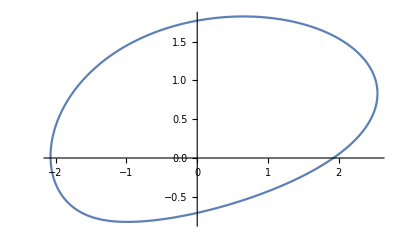

```mathematica
ListLinePlot[GetNumRange[{{1, 1, 1}, {2, I, 1}, {1, 2I, -1}}]]
```

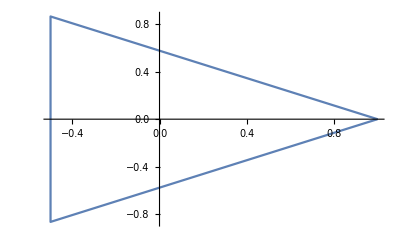

```mathematica
ListLinePlot[GetNumRange[{{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 1, 0, 0}, {0, 0, 1, 0}}]]
```